```mathematica
(* Сковлюк Г.Р. 221701 Вариант 4*)
(* Задание 1 *)
(* а) *)
```

```mathematica
f[x_,y_]=Cos[2x+y]+x-y;x0=0;y0=0;a=0;b=1;h=0.1;n=(b-a)/h;
x=x0;y=y0; eultmp1=Table[{x+i*h,y+i*h*f[x,y]},{i,1,n}];
eultmp1=Prepend[eultmp1,{x0,y0}]
```

{{0,0},{0.1,0.1},{0.2,0.2},{0.3,0.3},{0.4,0.4},{0.5,0.5},{0.6,0.6},{0.7,0.7},{0.8,0.8},{0.9,0.9},{1.,1.}}

```mathematica
Koshi1 = Table[{x+i*h,y+i*h+h/2(f[x,y]+f[x+i*h,eultmp1[[i,2]]])},{i,1,n}];
Koshi1=Prepend[Koshi1,{x0,y0}]
```

{{0,0},{0.1,0.2},{0.2,0.3},{0.3,0.4},{0.4,0.5},{0.5,0.6},{0.6,0.7},{0.7,0.8},{0.8,0.9},{0.9,1.},{1.,1.1}}

```mathematica
(* б) *)
```

```mathematica
Runge1=List[{x0,y0}]
x=x0;y=y0;
For[k=1,k<=n,k++,
k1[x_,y_]:=h*f[x,y];
k2[x_,y_]:=h*f[x+h/2,y+k1[x,y]/2];
k3[x_,y_]:=h*f[x+h/2,y+k2[x,y]/2];
k4[x_,y_]:=h*f[x+h,y+k3[x,y]];
x=x+h;y=y+(k1[x,y]+2k2[x,y]+2k3[x,y]+k4[x,y])/6;
Runge1=Append[Runge1,{x,y}];]
Runge1
```

{{0,0},{0.1,0.1},{0.2,0.2},{0.3,0.3},{0.4,0.4},{0.5,0.5},{0.6,0.6},{0.7,0.7},{0.8,0.8},{0.9,0.9},{1.,1.}}

```mathematica
(* в) *)
```

```mathematica
Clear[x,y]
dsolvemethod1=DSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],x];
dsolvemethodFunc[x_]=y[x]/.Flatten[dsolvemethod1]
```

```mathematica
ndsolvemethod1=NDSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],{x,0,1}];
```

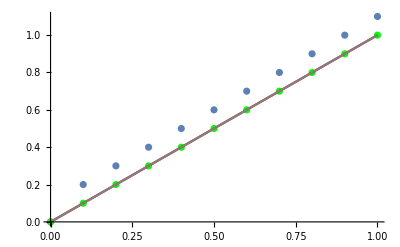

```mathematica
Koshigraph1=ListPlot[Koshi1];
Rungegraph1=ListPlot[Runge1,PlotStyle->Green];
dsolvegraph1=Plot[dsolvemethodFunc[x],{x,0,1},ImageSize->Small,PlotStyle->Red];
ndsolvegraph1=Plot[Evaluate[y[x]/.ndsolvemethod1],{x,0,1},ImageSize->Small, PlotStyle->Gray];
Show[Koshigraph1,Rungegraph1,dsolvegraph1,ndsolvegraph1]
```

```mathematica
Clear[n,h,x,y]
```

```mathematica
h=0.05;n=(b-a)/h;
```

20.

```mathematica
(* а) *)
```

```mathematica
x=x0;y=y0; eultmp2=Table[{x+i*h,y+i*h*f[x,y]},{i,1,n}];
eultmp2=Prepend[eultmp2,{x0,y0}]
```

{{0,0},{0.05,0.05},{0.1,0.1},{0.15,0.15},{0.2,0.2},{0.25,0.25},{0.3,0.3},{0.35,0.35},{0.4,0.4},{0.45,0.45},{0.5,0.5},{0.55,0.55},{0.6,0.6},{0.65,0.65},{0.7,0.7},{0.75,0.75},{0.8,0.8},{0.85,0.85},{0.9,0.9},{0.95,0.95},{1.,1.}}

```mathematica
Koshi2 = Table[{x+i*h,y+i*h+h/2(f[x,y]+f[x+i*h,eultmp2[[i,2]]])},{i,1,n}];
Koshi2=Prepend[Koshi2,{x0,y0}]
```

{{0,0},{0.05,0.1},{0.1,0.15},{0.15,0.2},{0.2,0.25},{0.25,0.3},{0.3,0.35},{0.35,0.4},{0.4,0.45},{0.45,0.5},{0.5,0.55},{0.55,0.6},{0.6,0.65},{0.65,0.7},{0.7,0.75},{0.75,0.8},{0.8,0.85},{0.85,0.9},{0.9,0.95},{0.95,1.},{1.,1.05}}

```mathematica
(* б) *)
```

```mathematica
Runge2=List[{x0,y0}];
x=x0;y=y0;
For[k=1,k<=n,k++,
k1[x_,y_]:=h*f[x,y];
k2[x_,y_]:=h*f[x+h/2,y+k1[x,y]/2];
k3[x_,y_]:=h*f[x+h/2,y+k2[x,y]/2];
k4[x_,y_]:=h*f[x+h,y+k3[x,y]];
x=x+h;y=y+(k1[x,y]+2k2[x,y]+2k3[x,y]+k4[x,y])/6;
Runge2=Append[Runge2,{x,y}];];
```

```mathematica
Runge2
```

{{0,0},{0.05,0.05},{0.1,0.1},{0.15,0.15},{0.2,0.2},{0.25,0.25},{0.3,0.3},{0.35,0.35},{0.4,0.4},{0.45,0.45},{0.5,0.5},{0.55,0.55},{0.6,0.6},{0.65,0.65},{0.7,0.7},{0.75,0.75},{0.8,0.8},{0.85,0.85},{0.9,0.9},{0.95,0.95},{1.,1.}}

```mathematica
(* в) *)
```

```mathematica
Clear[x,y]
dsolvemethod2=DSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],x];
dsolvemethodFunc2[x_]=y[x]/.Flatten[dsolvemethod2];
```

```mathematica
ndsolvemethod2=NDSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],{x,0,1}];
```

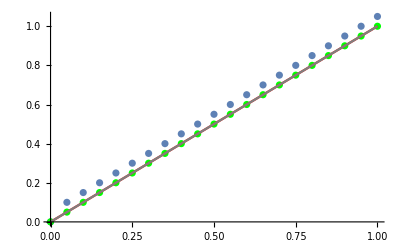

```mathematica
Koshigraph2=ListPlot[Koshi2];
Rungegraph2=ListPlot[Runge2,PlotStyle->Green];
dsolvegraph2=Plot[dsolvemethodFunc2[x],{x,0,1},ImageSize->Small,PlotStyle->Red];
ndsolvegraph2=Plot[Evaluate[y[x]/.ndsolvemethod2],{x,0,1},ImageSize->Small, PlotStyle->Gray];
Show[Koshigraph2,Rungegraph2,dsolvegraph2,ndsolvegraph2]
```

```mathematica
(*Вывод: при уменьшении шага h (h->0) значение дифференциала точнее ввиду уменьшения погрешности*)
```

```mathematica
(* Задание 2 *)
```

```mathematica
f[y_,z_]=y+2z;
g[y_,z_]=f[y,z]-3y-1;
x0=0;y[x0]=0;z[x0]=0;a=0;b=1;
```

```mathematica
h=0.1;n=(b-a)/h;
```

```mathematica
(* а) *)
```

```mathematica
Do[
y[i+1]=y[i]+h*f[y[i],z[i]];
z[i+1]=z[i]+h*g[y[i],z[i]];,{i,0,1/h}]

EulerYgraph1=ListLinePlot[Table[{i*h,y[i]},{i,0,1/h}],PlotStyle->Green];
EulerZgraph1 = ListLinePlot[Table[{i*h,z[i]},{i,0,1/h}],PlotStyle->Green];
```

```mathematica
(* б) *)
```

```mathematica
Clear[y,z];
y[x0]=0;z[x0]=0;
```

```mathematica
Do[
k1=h*f[y[i],z[i]];
l1=h*(y[i]-z[i]);
k2=h*f[y[i]+h/2,z[i]+l1/2];
l2=h*g[y[i]+h/2,z[i]+k1/2];
k3=h*f[y[i]+h/2,z[i]+l2/2];
l3=h*g[y[i]+h/2,z[i]+k2/2];
k4=h*f[y[i]+h,z[i]+l3];
l4=h*g[y[i]+h,z[i]+k3];
y[i+1]=y[i]+1/6*(k1+2*k2+2*k3+k4);
z[i+1]=z[i]+1/6*(l1+2*l2+2*l3+l4);,{i,0,1/h}]
RungeYgraph1=ListLinePlot[Table[{i*h,y[i]},{i,0,1/h}],PlotStyle->Red];
RungeZgraph1=ListLinePlot[Table[{i*h,z[i]},{i,0,1/h}],PlotStyle->Red];
```

```mathematica
(* в) *)
```

```mathematica
Clear[y,z];
```

```mathematica
solvemethod1=NDSolve[{y'[x]+2z[x]==0,z'[x]-3y'[x]-1==0,y[0]==0,z[0]==0},{y,z},{x,a,b}];
solvemethod2=DSolve[{y'[x]+2z[x]==0,z'[x]-3y'[x]-1==0,y[0]==0,z[0]==0},{y,z},x];
DSolvegraph1=ParametricPlot[Evaluate[{y[x],z[x]}/.solvemethod2],{x,0,1},PlotStyle->Green];
NDSolvegraph1=ParametricPlot[Evaluate[{y[x],z[x]}/. solvemethod1],{x,0,1},PlotStyle->Red];
```

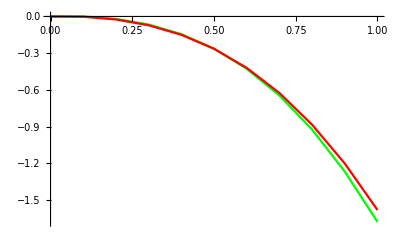

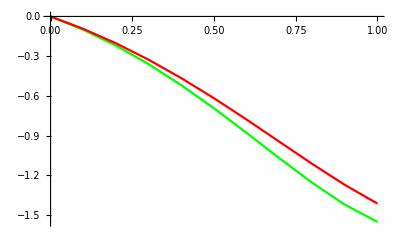

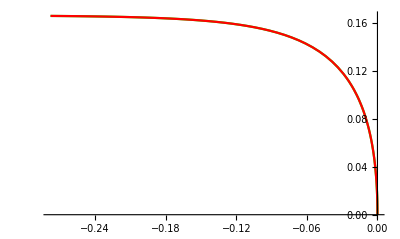

```mathematica
Show[EulerYgraph1,RungeYgraph1]
Show[EulerZgraph1,RungeZgraph1]
Show[DSolvegraph1,NDSolvegraph1]
```

```mathematica
h=0.05;n=(b-a)/h;
```

```mathematica
(* а) *)
```

```mathematica
Clear[x,y,z];
y[x0]=0;z[x0]=0;
```

```mathematica
Do[
y[i+1]=y[i]+h*f[y[i],z[i]];
z[i+1]=z[i]+h*g[y[i],z[i]];,{i,0,1/h}]

EulerYgraph2=ListLinePlot[Table[{i*h,y[i]},{i,0,1/h}],PlotStyle->Green];
EulerZgraph2= ListLinePlot[Table[{i*h,z[i]},{i,0,1/h}],PlotStyle->Green];
```

```mathematica
(* б) *)
```

```mathematica
Clear[y,z];
y[x0]=0;z[x0]=0;
```

```mathematica
Do[
k1=h*f[y[i],z[i]];
l1=h*(y[i]-z[i]);
k2=h*f[y[i]+h/2,z[i]+l1/2];
l2=h*g[y[i]+h/2,z[i]+k1/2];
k3=h*f[y[i]+h/2,z[i]+l2/2];
l3=h*g[y[i]+h/2,z[i]+k2/2];
k4=h*f[y[i]+h,z[i]+l3];
l4=h*g[y[i]+h,z[i]+k3];
y[i+1]=y[i]+1/6*(k1+2*k2+2*k3+k4);
z[i+1]=z[i]+1/6*(l1+2*l2+2*l3+l4);,{i,0,1/h}]
RungeYgraph2=ListLinePlot[Table[{i*h,y[i]},{i,0,1/h}],PlotStyle->Red];
RungeZgraph2=ListLinePlot[Table[{i*h,z[i]},{i,0,1/h}],PlotStyle->Red];
```

```mathematica
(* в) *)
```

```mathematica
Clear[y,z,solvemethod1,solvemethod2]
```

```mathematica
solvemethod1=NDSolve[{y'[x]==-y[x]+2z[x],z'[x]==-2y'[x]-5z[x],y[0]==0,z[0]==1},{y,z},{x,a,b}];
solvemethod2=DSolve[{y'[x]==-y[x]+2z[x],z'[x]==-2y'[x]-5z[x],y[0]==0,z[0]==1},{y,z},x];
DSolvegraph2=ParametricPlot[Evaluate[{y[x],z[x]}/.solvemethod2],{x,0,1},PlotStyle->Green];
NDSolvegraph2=ParametricPlot[Evaluate[{y[x],z[x]}/. solvemethod1],{x,0,1},PlotStyle->Red];
```

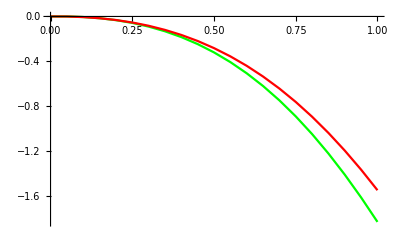

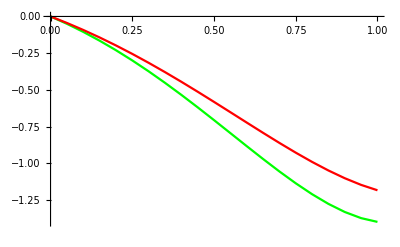

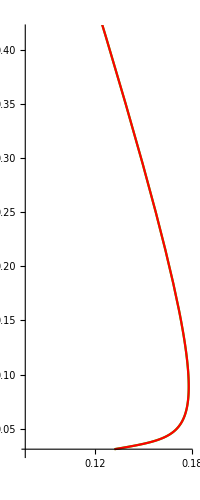

```mathematica
Show[EulerYgraph2,RungeYgraph2]
Show[EulerZgraph2,RungeZgraph2]
Show[DSolvegraph2,NDSolvegraph2]
```